Trabalho em Grupo Opcional: Campo Elétrico

Sylvio Barreto Veras- 2019200446
Mahathma Ghibran Caetano- 2021101272

1-Use o software Wolfram Mathematica para calcular a integral que resulta na expressão do campo elétrico E⃗ (ρ, θ, z), para uma linha de cargas infinita, com densidade linear constante λ0 é :

```mathematica
integrando=1/ρ;
integral=Integrate[integrando,ρ]
```

Log[ρ]

Use o software Wolfram Mathematica para fazer gráfico de :

a) módulo do campo elétrico E(ρ) × ρ:

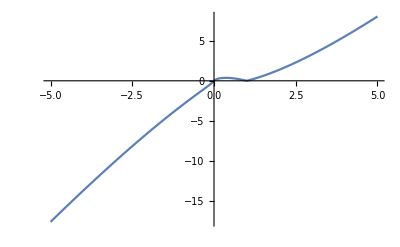

```mathematica
a=-5;
b=5;
Plot[Abs[integral]*ρ,{ρ,a,b}]
```

b)campo vetorial de E⃗ no plano:

Log[ρ]

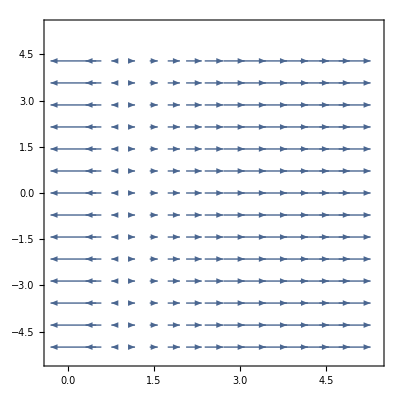

```mathematica
integrando=1/ρ;
integral=Integrate[integrando,ρ]
a=0.1;
b=5;
c=-5;
d=5;
VectorPlot[{Re[integral],Im[integral]},{ρ,a,b},{z,c,d}]
```

c) campo vetorial de E⃗ no espaço 3D:

```mathematica
a=-5;
b=5;
c=-5;
d=5;
e=-5;
f=5;
VectorPlot3D[{Re[integral],Im[integral],0},{ρ,a,b},{z,c,d},{θ,e,f}]
```

-Graphics3D-

2-Use o software Wolfram Mathematica para calcular a integral na expressão do campo elétrico E⃗ , sobre um ponto z arbitrário do eixo do anel carregado (usualmente eixo z) com uma densidade de cargas linear constante :

```mathematica
Integrate[z/((z^2+1)^(3/2)),z]
```

-1/(√(1+z^2))

Use o software Wolfram Mathematica para fazer gráfico de :

a) E(z) × z:

```mathematica
Plot[Evaluate[-1/((z^2+1)^(1/2))],{z,-10,10},AxesLabel->{"z","E(z) * z"},PlotLabel->"E(z) * z vs. z (Q = 1, R = 1)"]
```

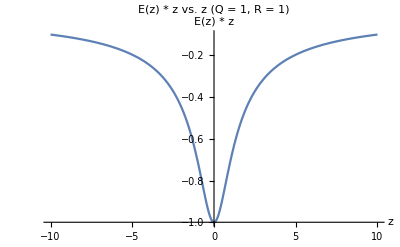

b) E(z, R) × (z, R):

```mathematica
Manipulate[Plot[Evaluate[(Q*(-z))/((z^2+R^2)^(1/2))],{z,-10,10},AxesLabel->{"z","E(z) * z"},PlotLabel->"E(z) * z vs. z (Q = "<>ToString[Q]<>", R = "<>ToString[R]<>")"],{{Q,1,"Q (Carga)"},0.1,10},{{R,1,"R (Raio)"},0.1,10}]
```